54010./(8888.31+1982.96/(2.42105+1/Kamp)^4)

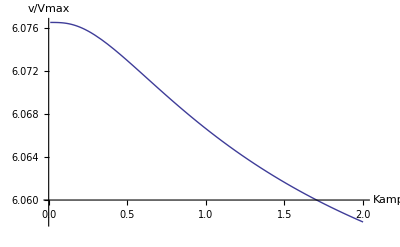

```mathematica
vdividedbyVmax= (pep adp (pep/Kpep+1)^n)/(Kpep (L((1+atp/Katp)/(fdp/Kfdp+amp/Kamp+1))^n+(pep/Kpep+1)^n)(adp+Kadp));
parm={Kpep->0.31,Kadp->0.26,Kfdp->0.19,Katp->22.5,L->1000,n->4,pep->2.7,atp->4.2,adp->0.6,amp->1, fdp->0.27,Vmax->1};
vdividedbyVmax/.parm
Plot[%,{Kamp,0.01,2},AxesLabel->{"Kamp","v/Vmax"},PlotRange->All]
```

Changing the Kamp around the set value of 0.2 mM has only little effect on the rate of the enzyme; watch the little changes in the y-axis.  So even though this value was estimated and not known, it is also not important in value!